```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\fastm\res

```mathematica
n=128;
```

```mathematica
Sol=Flatten[Import["gamRes.txt","Table"]][[;;-2]]
```

{-0.102231,-0.0618434,-0.0563586,-0.0538524,-0.0528834,-0.0528773,-0.0536611,-0.0552365,-0.0577235,-0.0613555,-0.0664945,-0.0736397,-0.0833648,-0.096013,-0.110844,-0.124651,-0.131684,-0.127789,-0.115022,-0.0992321,-0.0847521,-0.0730794,-0.0641272,-0.057335,-0.0521392,-0.0480966,-0.0448844,-0.0422742,-0.0401043,-0.0382598,-0.0366575,-0.0352364,-0.0339512,-0.0327673,-0.0316579,-0.0306019,-0.0295822,-0.0285847,-0.0275973,-0.0266094,-0.0256115,-0.0245947,-0.0235504,-0.0224698,-0.0213439,-0.0201631,-0.0189169,-0.0175932,-0.0161781,-0.0146552,-0.0130046,-0.0112015,-0.009215,-0.00700475,-0.00451746,-0.00168041,0.001609,0.00550137,0.0102289,0.0161725,0.0240107,0.0350932,0.0525384,0.0843,0.130128,0.148054,0.124856,0.102959,0.0896234,0.0806551,0.0740856,0.0689837,0.0648548,0.0614106,0.05847,0.0559133,0.0536575,0.0516431,0.049826,0.0481728,0.0466576,0.0452601,0.0439639,0.0427556,0.0416242,0.0405607,0.0395574,0.0386075,0.0377057,0.0368469,0.0360269,0.035242,0.0344888,0.0337645,0.0330662,0.0323916,0.0317385,0.0311048,0.0304885,0.0298878,0.029301,0.0287264,0.0281624,0.0276072,0.0270592,0.0265166,0.0259777,0.0254404,0.0249028,0.0243626,0.0238171,0.0232628,0.0226956,0.0221113,0.0215051,0.0208703,0.0201981,0.0194768,0.0186905,0.0178176,0.0168261,0.0156675,0.0142629,0.0124737,0.0100267,0.00627509,-0.000277121,-0.0414887,0.0887021,0.00719112,0.00355105,0.0015257,0.000407988,-0.000418604,-0.0011815,-0.00201103,-0.00301668,-0.00431733,-0.0060505,-0.00834517,-0.0111919,-0.0140647,-0.0152212,-0.011592,-0.00184757,0.00928729,0.0153543,0.0156409,0.0131523,0.0102269,0.00776149,0.00590069,0.00454946,0.00357724,0.00287524,0.00236399,0.00198796,0.0017089,0.00150042,0.00134414,0.0012272,0.00114043,0.00107728,0.00103301,0.0010042,0.000988355,0.000983714,0.000989045,0.00100355,0.00102679,0.00105865,0.0010993,0.00114921,0.00120919,0.00128041,0.00136451,0.0014637,0.00158098,0.00172041,0.00188752,0.00209006,0.00233902,0.00265047,0.00304875,0.00357219,0.0042844,0.00529789,0.00682885,0.00934119,0.0139923,0.0243055,0.0517602,0.0612209,-0.0346272,-0.0376152,-0.0193562,-0.0117305,-0.00807007,-0.00601721,-0.0047343,-0.00386924,-0.00325254,-0.0027939,-0.00244131,-0.00216294,-0.00193831,-0.00175372,-0.00159969,-0.00146948,-0.00135814,-0.00126202,-0.00117832,-0.0011049,-0.00104007,-0.000982519,-0.000931164,-0.000885147,-0.000843767,-0.000806445,-0.000772705,-0.000742151,-0.000714455,-0.000689342,-0.000666585,-0.000645997,-0.000627424,-0.000610744,-0.000595863,-0.000582712,-0.00057125,-0.000561461,-0.000553353,-0.000546965,-0.000542362,-0.000539631,-0.000538883,-0.000540276,-0.000544121,-0.000551023,-0.000561745,-0.00057669,-0.000596061,-0.000620936,-0.00065345,-0.000696183,-0.00075236,-0.000826799,-0.000927151,-0.00106598,-0.00126503,-0.00156484,-0.00204882,-0.00291398,-0.00476181,-0.00831994,-0.0896884}

```mathematica
SolNumPNL[t_?NumberQ]:=Module[{xt,yt,rt,q,St},
 q=1;While[t>q+1,q++];
rt=t-q;
Sol[[q]]+Sol[[n+q]]*(rt-1/2)
]
```

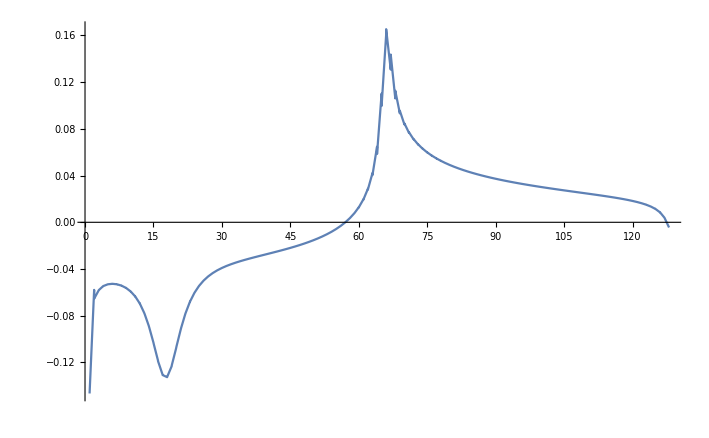

```mathematica
Plot[SolNumPNL[t],{t,1,128},PlotPoints->1000]
```